# Test and Filter Runs

n: number of stars
NS: number of simulations
R: virial radius
Isolated System

### Logs

```mathematica
Print[$RunNumber]
```

100

```mathematica
Print[script`path]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest

```mathematica
logstream = OpenWrite[
FileNameJoin[{script`path, "nbstatus" <> ToString[$RunNumber] <> ".log"}],
FormatType->OutputForm
]
```

OutputStream[…]

```mathematica
Write[logstream, "Begin log ...."];
```

## Initialization

```mathematica
{$MachineName,$Version}
```

{tars,12.1.0 for Linux x86 (64-bit) (March 18, 2020)}

```mathematica
AppendTo[$Path,Environment["MYGITDIR"]];
```

```mathematica
Get["AstroTools`nbody6`"]
```

```mathematica
Get["AstroTools`Utilities`"]
```

```mathematica
$ConfiguredKernels = 
 List[SubKernels`LocalKernels`LocalMachine[30, 
   Rule[SubKernels`LocalKernels`LowerPriority, True]]]
```

{SubKernels`LocalKernels`LocalMachine[30,SubKernels`LocalKernels`LowerPriority→True]}

```mathematica
resultsPath=FileNameJoin[{Environment["MYGITDIR"],"workspace","nbody6","isolated","n"<>ToString[$RunNumber],"NSX-R1","results"}]
```

/home/cesarg/git/workspace/nbody6/isolated/n100/NSX-R1/results

```mathematica
SetDirectory[resultsPath]
```

/home/cesarg/git/workspace/nbody6/isolated/n100/NSX-R1/results

```mathematica
FileNames[]
```

{goodRuns.log,run-102,run-105,run-108,run-11,run-123,run-125,run-134,run-137,run-140,run-141,run-155,run-159,run-160,run-174,run-176,run-178,run-18,run-187,run-194,run-198,run-20,run-206,run-214,run-229,run-231,run-24,run-241,run-243,run-244,run-25,run-253,run-255,run-258,run-262,run-264,run-266,run-268,run-282,run-284,run-289,run-292,run-31,run-313,run-314,run-322,run-335,run-344,run-36,run-360,run-363}

### n–body parameters

```mathematica
(*
numberOfStars=380;
nb["S0"]=0.3(numberOfStars/1000)^(1/3)
nb["nMAX"]=2.(numberOfStars)^(1/2)
*)
```

```mathematica
FilePrint["../create-ini.sh"]
```

#!/bin/bash
# series 1-500

echo "[`date`] Start"

mkdir results

cd results/
for filenumber in {1..500..1}
do
	mkdir "./run-$filenumber/"
  	cat << EOF > ./run-$filenumber/ini.dat
1 20.0
100 1 10 $RANDOM 24 1
0.02 0.01 0.14 2.0 1.0 701.0 1.0E-03 1 0.5
0 0 1 0 1 0 0 0 0 0
0 0 0 0 0 0 0 0 0 6
0 0 0 0 0 0 0 0 0 0
0 0 0 0 0 0 0 0 0 1
0 0 0 0 0 0 0 0 0 0
4.0E-05 0.001 0.2 1.0 1.0E-06 0.001
2.3 50.0 0.1 0 0 0.002 0 5.0
0.5 0 0 0 0.5
EOF

done

cd ..
echo `pwd`
echo "[`date`] End"
echo "time elapsed: $SECONDS"
echo all done

```mathematica
strCreateFile=Import["../create-ini.sh","Table"]
```

{{#!/bin/bash},{#,series,1-500},{},{echo,[`date`] Start},{},{mkdir,results},{},{cd,results/},{for,filenumber,in,{1..500..1}},{do},{mkdir,./run-$filenumber/},{cat,<<,EOF,>,./run-$filenumber/ini.dat},{1,20.},{100,1,10,$RANDOM,24,1},{0.02,0.01,0.14,2.,1.,701.,0.001,1,0.5},{0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,6},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0},{0.00004,0.001,0.2,1.,1.×10^-6,0.001},{2.3,50.,0.1,0,0,0.002,0,5.},{0.5,0,0,0,0.5},{EOF},{},{done},{},{cd,..},{echo,`pwd`},{echo,[`date`] End},{echo,time elapsed: $SECONDS},{echo,all,done}}

```mathematica
pos=Position[strCreateFile,"$RANDOM"][[1,1]];
numberOfStars=strCreateFile[[pos,1]]
nbodyStep=Floor@(strCreateFile[[pos+1,5]])
maxNbodyTime=Floor@(strCreateFile[[pos+1,6]]-nbodyStep)
```

100

1

700

### Other global variables

#### Data

```mathematica
goodFiles=FileNameJoin[First[#]]&/@GatherBy[StringSplit[Import["goodRuns.log"][[All,2]],"/"],#[[-2]]&];
```

```mathematica
dirs=DirectoryName/@goodFiles;
```

```mathematica
runmax=Length[dirs]
```

50

```mathematica
If[!FileExistsQ["nbody6-data.mx"]
,
Print["Loading from source ..."];
data=ReadOutput/@goodFiles;
DumpSave["nbody6-data.mx",data];
,
Print["Loading from MX ..."];
Get["nbody6-data.mx"];
]//AbsoluteTiming
```

Loading from source ...

ReadList::readn: Invalid real number found when reading from «1».

General::stop: Further output of «1» will be suppressed during this calculation.

{11.4012,Null}

```mathematica
parameters=data[[All,1]];
```

```mathematica
parameters//Length
```

50

```mathematica
data=data[[All,2]];
```

```mathematica
lengthOfRuns=Tally[Length/@data]
```

{{701,50}}

#### Parameters

```mathematica
(* NOTE 1: parameters V^*, T^*, M^* are different for each run *)
(* NOTE 2: $MeanMass numberOfStats ≈ $MassScale *)
parameters[[All,4]]
```

{2.113,1.453,2.513,2.078,1.813,1.487,2.359,1.902,1.887,2.494,2.022,2.151,2.036,2.325,1.922,2.361,2.332,2.083,2.071,2.253,2.505,2.342,2.024,2.355,1.71,1.933,2.076,2.152,2.056,2.094,2.103,2.205,1.889,1.809,1.803,1.92,2.343,2.345,2.169,2.001,2.275,1.943,2.277,2.12,2.244,2.227,1.954,2.095,1.807,1.66}

```mathematica
{$LengthScale,$MassScale,$SpeedScale,$TimeScale,$MeanMass,$SU}=Mean[parameters]
```

{1.,53.656,0.47652,2.08182,0.5362,4.4×10^7}

```mathematica
$EnergyScale=$MassScale ($SpeedScale)^2
```

12.1837

```mathematica
$DensityScale=$MassScale/($LengthScale)^3
```

53.656

```mathematica
(* in units of Msun/pc^3*)
ρSunNeighborPhysical=0.09;
ρForClusterDisruptionPhysical=0.08;
```

```mathematica
(* in units of n-body units *)
ρSunNeighbor=ρSunNeighborPhysical/$DensityScale;
ρForClusterDisruption=ρForClusterDisruptionPhysical/$DensityScale;
```

```mathematica
(* checking units *)
ρSunNeighbor
```

0.00167735

```mathematica
(* mean density in nbody units *)
$MeanDensity=1./(4/3Pi(1)^3)
```

0.238732

```mathematica
(* mean density physical Msun/pc^3 *)
$MeanDensity $DensityScale
```

12.8094

```mathematica
(* Max elpased time for evolution in MY*)
maxNbodyTime*$TimeScale
```

1457.27

```mathematica
(* INITIAL TIME = 0 -> following nbody6 *)
timeArray=Range[0,maxNbodyTime,nbodyStep];
(* log step array: 0 time at -1 *)
log10TimeArray1=N@Prepend[Log10[Rest[timeArray]],0];
log10TimeArrayScaled1=N@Prepend[Log10[Rest[$TimeScale timeArray]],0];
```

```mathematica
Length/@{timeArray,log10TimeArray1,log10TimeArrayScaled1}
```

{701,701,701}

## Delete invalid runs

```mathematica
dirsToDelete=Complement[Select[FileNames[],DirectoryQ],Part[StringSplit[#,$PathnameSeparator]&/@dirs,All,2]];
```

```mathematica
dirsToDelete=Flatten[StringCases[dirsToDelete,"run-"~~__]];
```

```mathematica
dirsToDelete//Short
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
(*Table[Style[Import[StringTemplate["!tail -n 2 ``/output"][dirsToDelete[[j]]],"String"],If[OddQ[j],Blue,Brown]],{j,Length@dirsToDelete}]//ColumnForm*)
```

```mathematica
If[Length[dirsToDelete]≠0,
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete,
Print["Nothing to delete"]]
```

Nothing to delete

## run cpu timings

```mathematica
Directory[]
```

/home/cesarg/git/workspace/nbody6/isolated/n100/NSX-R1/results

```mathematica
timingFiles=FileNames["run*/timings"];
timingFiles//Short
```

{run-102/timings,run-105/timings,run-108/timings,run-11/timings,run-123/timings,run-125/timings,run-134/timings,run-137/timings,run-140/timings,run-141/timings,run-155/timings,run-159/timings,run-160/timings,run-174/timings,run-176/timings,run-178/timings,run-187/timings,run-18/timings,run-194/timings,run-198/timings,run-206/timings,run-20/timings,run-214/timings,run-229/timings,run-231/timings,run-241/timings,run-243/timings,run-244/timings,run-24/timings,run-253/timings,run-255/timings,run-258/timings,run-25/timings,run-262/timings,run-264/timings,run-266/timings,run-268/timings,run-282/timings,run-284/timings,run-289/timings,run-292/timings,run-313/timings,run-314/timings,run-31/timings,run-322/timings,run-335/timings,run-344/timings,run-360/timings,run-363/timings,run-36/timings}

```mathematica
timeStrings=Cases[Import[#],{"real",_}][[1,2]]&/@timingFiles;
timeStrings//Short
```

{0m7.568s,0m2.818s,0m6.051s,0m7.043s,0m6.501s,0m5.541s,0m4.943s,0m2.630s,0m4.755s,0m6.335s,0m3.799s,0m10.323s,0m8.166s,0m5.141s,0m3.270s,0m3.732s,0m2.068s,0m6.272s,0m2.061s,0m8.075s,0m7.693s,0m8.405s,0m7.719s,0m4.743s,0m4.135s,0m6.909s,0m2.715s,0m7.718s,0m5.352s,0m6.093s,0m5.336s,0m4.587s,0m7.208s,0m2.928s,0m2.722s,0m6.496s,0m8.136s,0m6.700s,0m9.376s,0m7.660s,0m7.619s,0m3.566s,0m4.032s,0m11.274s,0m8.258s,0m5.037s,0m3.177s,0m4.664s,0m4.584s,0m4.507s}

```mathematica
timeElapsedStringToSeconds[string_]:=(60#1+#2)&@@ToExpression[StringSplit[string,"m"|"s"]]
```

```mathematica
timings=timeElapsedStringToSeconds/@timeStrings;
```

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@Mean[timings]
```

Set::write: Tag «12» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

SetDelayed::write: Tag «11» in «1» is Protected.

General::stop: Further output of «1» will be suppressed during this calculation.

5.72882 s

```mathematica
If[#>60,Quantity[#/60,"Minutes"],Quantity[#,"Seconds"]]&@StandardDeviation[timings]
```

2.19903 s

## n–body results

### Mean rhalf

```mathematica
meanRhalf=Mean/@DeleteCases[Transpose[data[[All,All,1]]],$Failed,{2}];
```

```mathematica
meanRhalfAndTime=Transpose[{timeArray,meanRhalf}];
```

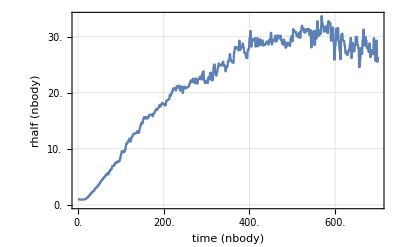

```mathematica
meanRhalfAndTimePlot=ScaledListPlot[meanRhalfAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rhalf (nbody)","rhalf (pc)"},{"time (nbody)","time (My)"}},
"ShowAllScales"->True]
```

### Mean rdens

```mathematica
meanRdens=Mean/@DeleteCases[Transpose[data[[All,All,3]]],$Failed,{2}];
```

```mathematica
meanRdensAndTime=Transpose[{timeArray,meanRdens}];
```

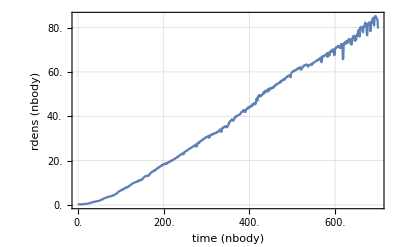

```mathematica
meanRdensAndTimePlot=ScaledListPlot[meanRdensAndTime,{$TimeScale,$LengthScale},
FrameLabel->{{"rdens (nbody)","rdens (pc)"},{"time (nbody)","time (My)"}},"ShowAllScales"->True]
```

## Loading Data

#### Load from OUT3 or MX

```mathematica
(* 8 values: id, pos, vel, mass *)
(* 8 bytes each one *)
```

```mathematica
(numberOfStars*maxNbodyTime*runmax*8*8)/(1024*1024*1024. nbodyStep)
```

0.208616

```mathematica
snapshots=All;
```

```mathematica
(*snapshots=Range[1,maxNbodyTime,10];*)
```

```mathematica
Write[logstream, "computing particles.mx ...."]
```

```mathematica
(* Check also: "particles.bin" *)
If[!FileExistsQ["particles.mx"]
	,
	Print[TimeAndMem[]];
	(*While[Kernels[] == {}, 
		kernels = LaunchKernels[];
		];*)
	kernels = LaunchKernels[];
	Write[logstream, kernels];
	Print["Kernels: ", kernels];
	SetSharedVariable[dirs];
	ParallelEvaluate[AppendTo[$Path, Environment["MYGITDIR"]]];
	ParallelEvaluate[SetDirectory[resultsPath]];
	ParallelNeeds["AstroTools`nbody6`"];
	ParallelNeeds["AstroTools`Utilities`"];
	(particles = 
		Transpose@
		ParallelTable[
			SetDirectory[dirs[[i]]];
			Print["DIR: ", dirs[[i]]];
			{bodys,xs,vs,name} = Flatten[ReadOUT3["OUT3","Snapshots" -> snapshots], 1];
			xs=Partition[#,3]&/@xs;
			vs=Partition[#,3]&/@vs;
			ResetDirectory[]; 
			{bodys,xs,vs,name}
			,
			{i,1,Length[dirs]}]);
	
	Print["Closing kernels ..."];
	CloseKernels[];

	(*-- SAVE to a MX file --*)
	Print["Saving data to MX ... "];
	Print[TimeAndMem[]];
	DumpSave["particles.mx", particles];
	Print[TimeAndMem[]];

	(*-- SAVE to a BIN file --*)
	(* BinarySerializeSave[particles,"particles.bin"]; // AbsoluteTiming *)
	
	,
	
	(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["particles.mx"];
] // AbsoluteTiming
```

15:36:18 mem:151.726MB

Kernels: {KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

DIR: ./run-102/

DIR: ./run-108/

DIR: ./run-123/

DIR: ./run-134/

DIR: ./run-140/

DIR: ./run-155/

DIR: ./run-160/

DIR: ./run-176/

DIR: ./run-187/

DIR: ./run-194/

DIR: ./run-206/

DIR: ./run-214/

DIR: ./run-231/

DIR: ./run-243/

DIR: ./run-24/

DIR: ./run-255/

DIR: ./run-25/

DIR: ./run-264/

DIR: ./run-268/

DIR: ./run-284/

DIR: ./run-292/

DIR: ./run-313/

DIR: ./run-314/

DIR: ./run-31/

DIR: ./run-322/

DIR: ./run-335/

DIR: ./run-344/

DIR: ./run-360/

DIR: ./run-363/

DIR: ./run-36/

DIR: ./run-241/

DIR: ./run-105/

DIR: ./run-11/

DIR: ./run-125/

DIR: ./run-137/

DIR: ./run-141/

DIR: ./run-159/

DIR: ./run-174/

DIR: ./run-178/

DIR: ./run-18/

DIR: ./run-198/

DIR: ./run-20/

DIR: ./run-229/

DIR: ./run-244/

DIR: ./run-253/

DIR: ./run-258/

DIR: ./run-262/

DIR: ./run-266/

DIR: ./run-282/

DIR: ./run-289/

Closing kernels ...

Saving data to MX ...

15:36:46 mem:1.05576GB

15:37:50 mem:954.993MB

{91.2966,Null}

```mathematica
Write[logstream, "particles.mx done!"]
```

```mathematica
(* --- serial computation ---
(particles=
Transpose@
Table[SetDirectory[dirs[[i]]];
Print["DIR: ", dirs[[i]]];
{bodys,xs,vs,name}=Flatten[ReadOUT3["OUT3","Snapshots"->All],1];
xs=Partition[#,3]&/@xs;
vs=Partition[#,3]&/@vs;
ResetDirectory[]; 
{bodys,xs,vs,name}
,{i,1,Length[dirs]}]);//AbsoluteTiming *)
```

#### Mem information

```mathematica
TimeAndMem[]
```

15:37:50 mem:954.995MB

```mathematica
(*PrintArrayInfo[particles]*)
```

```mathematica
DeleteOuts[500]
```

session mem: 954.999MB

No Out[] greater than 500MB

```mathematica
$numberOfRunsStatus=Dimensions[particles][[2]]
```

50

## Filtering Invalid Data

### Indexes To Extract Data

```mathematica
nbIndexes=Table[Range[maxNbodyTime/nbodyStep+1],{runmax}];
```

```mathematica
nbIndexes//Dimensions
```

{50,701}

```mathematica
nbIndexes[[1]]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701}

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

### Incomplete runs

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
Length/@particles[[4]]//Union
```

{701}

```mathematica
(* delete runs that have not complete data *)
maxtimes=Length/@particles[[4]]
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

```mathematica
delPos1=Position[maxtimes,x_/;x<Max[maxtimes]]
```

{}

```mathematica
delPos1//Length
```

0

#### FIX: Delete complete runs

```mathematica
Extract[dirs,delPos1]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos1],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete
```

{}

Opt – Update variables to continue computing

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
dirs=Delete[dirs,delPos1];
runmax=Length[dirs];
particles=Delete[#, delPos1]&/@particles;
nbIndexes=Delete[nbIndexes, delPos1];
nbLenIndexes=Length/@nbIndexes;
parameters=Delete[parameters, delPos1];
```

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
nbIndexes//Length
```

50

```mathematica
parameters//Dimensions
```

{50,6}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 980.43MB

### Particles in the same position

#### TEST

```mathematica
particles[[All,All,All,1;;numberOfStars]]//Dimensions
```

{4,50,701,100}

```mathematica
Clear[ceros];
If[!FileExistsQ["ceros.mx"],
ceros=Reap[
Do[
Print["run: ", run];
Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}];Print["CERO AT: ", run];Break[]]
]
,{t,1,nbLenIndexes[[run]]}
],
{run,1,runmax}]
];
DumpSave["ceros.mx", ceros]
,
(*-- Get file from MX --*)
	Print["Loading MX ..."];
	Get["ceros.mx"];
];//AbsoluteTiming
```

run: 1

run: 2

run: 3

run: 4

run: 5

run: 6

run: 7

run: 8

run: 9

run: 10

run: 11

run: 12

run: 13

run: 14

run: 15

run: 16

run: 17

run: 18

run: 19

run: 20

run: 21

run: 22

run: 23

run: 24

run: 25

run: 26

run: 27

run: 28

run: 29

run: 30

run: 31

run: 32

run: 33

run: 34

run: 35

run: 36

run: 37

run: 38

run: 39

run: 40

run: 41

run: 42

run: 43

run: 44

run: 45

run: 46

run: 47

run: 48

run: 49

run: 50

{25.924,Null}

```mathematica
ceros[[2]]
```

{}

#### Double check

```mathematica
(*invalid=With[{run=7},Reap[Do[
With[
{pe=TotalPotentialEnergy[particles[[1,run,t,All]],particles[[2,run,t,All]]]},
If[pe==0.,Sow[{run,t}]]
]
,{t,1,nbLenIndexes[[run]]}
]]
];*)
```

```mathematica
(*invalid//Short*)
```

```mathematica
(*With[{run=7, time=1100},
Select[GatherBy[Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}],Last],Length[#]>1&]]*)
```

```mathematica
(*With[
{part1=2,
part2=1,
run=46,
interTime=220
},
vel=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[3,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];
pos=Table[{#[part1],#[part2]}&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,run,time,All]],particles[[2,run,time,All]]}]|>),{time,1,nbLenIndexes[[run]],1}];

{ListLinePlot[{Norm/@vel[[All,1]],Norm/@vel[[All,2]]},
PlotRange->{{0,1000},{0,100}}],
ListLinePlot[{Norm/@pos[[All,1]],Norm/@pos[[All,2]]},
PlotRange->{{0,1000},{0,50000}},Epilog->InfiniteLine[{{interTime,0},{interTime,1}}]]}
]*)
```

```mathematica
(* testing indexes outside particles range *)
```

```mathematica
(*testing1001=Table[#[1001]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*Position[testimg1001,_Missing]*)
```

```mathematica
(*testing1002=Table[#[1002]&@(<|#[[1]]->#[[2]]&/@Transpose[{particles[[4,2,time,All]],particles[[2,2,time,All]]}]|>),{time,1,nbLenIndexes[[2]],1}];*)
```

```mathematica
(*testing1002[[8]]*)
```

#### FIX 1: Delete complete runs

```mathematica
delPos2=If[ceros[[2]]=={},{},Partition[Union[ceros[[2,1]][[All,1]]],1]];
```

```mathematica
delPos2//Short
```

{}

```mathematica
Extract[dirs,delPos2]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos2],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

(* 
	Si dirsToDelete≠0 borrar *.m *.mx 
	generar goodRuns.log y correr nb de nuevo.
*)

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos2];
```

```mathematica
runmax=Length[dirs]
```

50

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
particles=Delete[#, delPos2]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 980.43MB

```mathematica
nbIndexes=Delete[nbIndexes, delPos2];
```

```mathematica
nbIndexes//Length
```

50

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

```mathematica
parameters//Dimensions
```

{50,6}

```mathematica
parameters=Delete[parameters, delPos2];
```

```mathematica
parameters//Dimensions
```

{50,6}

#### FIX 2: Delete specific snapshots (ruled out)

```mathematica
(* We will delete data only for snapshots containg equal positions *)
```

delPos3 = ceros[[2, 1]]

particles = Delete[#, delPos3] & /@ particles;

timeIndexes[[1, 450]]

Complement[Range[1000], timeIndexes[[1]]]

timeIndexes = Delete[timeIndexes, delPos3];

Complement[Range[1000], timeIndexes[[1]]]

nbLenIndexes = Length /@ timeIndexes

### Particles with index 0 / position 0.

#### TEST

```mathematica
(* Delete time snaphots of incorrect data with ceros in the position vector. *)
(* Very strange issue from nbody *)
```

```mathematica
delPos4=Position[particles[[4]],0][[All,{1,2}]];
```

```mathematica
delPos4//Short
```

{}

```mathematica
delPos4[[All,1]]//Union
```

{}

```mathematica
delPos4[[All,1]]//Union//Length
```

0

```mathematica
(* NICE runs *)
Complement[Range[runmax],delPos4[[All,1]]//Union]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
(* Consistent with non missing IDs *)
moreIDS=Table[Position[Complement[Range[numberOfStars],#]&/@particles[[4,run,All,All]],x_/;x≠{},{1}],{run,runmax}];
Position[moreIDS,{}]//Flatten
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
bad=delPos4[[All,1]]//Union
good=Position[moreIDS,{}]//Flatten
```

{}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
(* Runs to be fixed: good + partOfBad = 50 *)
numToFix=Which[
Length[good]≥50,0,
Length[good]<50,50-Length[good]]
```

0

```mathematica
runsToFix=TakeSmallestBy[delPos4[[All,1]]//Tally,Last,UpTo[numToFix]]
```

{}

```mathematica
Complement[good,Take[good,50]]
```

{}

```mathematica
(* Runs to be deleted *)
runsToDelete=If[Length[good]≥50,
Union[bad,Complement[good,Take[good,50]]],
SortBy[Complement[delPos4[[All,1]]//Tally,runsToFix],Last][[All,1]]
]
```

{}

#### FIX Part–1: Delete complete runs

```mathematica
delPos5=Partition[runsToDelete,1]
```

{}

```mathematica
delPos5//Short
```

{}

```mathematica
delPos5//Length
```

0

```mathematica
Extract[dirs,delPos5]
```

{}

```mathematica
dirsToDelete=Part[StringSplit[#,$PathnameSeparator]&/@Extract[dirs,delPos5],All,2]
```

{}

```mathematica
dirsToDelete//Length
```

0

```mathematica
DeleteDirectory[#,DeleteContents->True]&/@dirsToDelete;
```

Opt 1 – Delete files to begin from scratch

FileNames["*.*"]

DeleteFile[#] & /@ FileNames["*.*"]

Opt 2 – Update variables to continue computing

```mathematica
dirs=Delete[dirs,delPos5]
```

{./run-102/,./run-105/,./run-108/,./run-11/,./run-123/,./run-125/,./run-134/,./run-137/,./run-140/,./run-141/,./run-155/,./run-159/,./run-160/,./run-174/,./run-176/,./run-178/,./run-187/,./run-18/,./run-194/,./run-198/,./run-206/,./run-20/,./run-214/,./run-229/,./run-231/,./run-241/,./run-243/,./run-244/,./run-24/,./run-253/,./run-255/,./run-258/,./run-25/,./run-262/,./run-264/,./run-266/,./run-268/,./run-282/,./run-284/,./run-289/,./run-292/,./run-313/,./run-314/,./run-31/,./run-322/,./run-335/,./run-344/,./run-360/,./run-363/,./run-36/}

```mathematica
runmax=Length[dirs]
```

50

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
particles=Delete[#, delPos5]&/@particles;
```

```mathematica
particles//Dimensions
```

{4,50,701}

```mathematica
PrintArrayInfo[particles]
```

Length: 4 MEM: 980.43MB

```mathematica
nbIndexes=Delete[nbIndexes, delPos5];
```

```mathematica
nbIndexes//Length
```

50

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

```mathematica
parameters//Dimensions
```

{50,6}

```mathematica
parameters=Delete[parameters, delPos5];
```

```mathematica
parameters//Dimensions
```

{50,6}

#### FIX Part–2: Delete specific snaphots

```mathematica
delPos6=Position[particles[[4]],0][[All,{1,2}]]
```

{}

```mathematica
delPos6[[All,1]]//Union
```

{}

```mathematica
%//Length
```

0

```mathematica
particles=Delete[#, delPos6]&/@particles;
```

```mathematica
nbIndexes=Delete[nbIndexes, delPos6];
```

```mathematica
nbLenIndexes=Length/@nbIndexes
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

```mathematica
nbLenIndexes//Length
```

50

### Position high values (test only)

With lack those cases happens together with the issues in the previous section. Fixing there makes fixed here.

highPos=Position[Map[Norm,particles[[2,All,1;;50,All]],{3}],x_/;x>10.^6]

particles[[2, 5, 4, 2]] // Norm

highPos[[All, 1]] // Union

## index ↔ nbIndex ↔ nbTime

```mathematica
Length/@nbIndexes
```

{701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701,701}

```mathematica
(* Indexes that are missing at least in one run *)
delPos6[[All,2]]//Union//Short
```

{}

```mathematica
%//Length
```

0

```mathematica
(* Indexes with complete data across runs *)
nbCompleteIndexes=Complement[Range[maxNbodyTime/nbodyStep+1],delPos6[[All,2]]//Union];
nbCompleteIndexes//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701}

```mathematica
(* Number of times with common data *)
nbCompleteIndexes//Length
```

701

```mathematica
(* Select a set of valid indexes with more or less equal spacing using nearest *)
```

```mathematica
(numberOfStars*numberOfStars*maxNbodyTime*runmax*1)/(1024*1024*1024. nbodyStep*10)
```

0.0325963

```mathematica
maxNbodyTime/nbodyStep
```

700

```mathematica
nbIndexesSubset=Flatten[Table[Nearest[nbCompleteIndexes,i,1],{i,0,maxNbodyTime/nbodyStep+1,5}]]
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600,605,610,615,620,625,630,635,640,645,650,655,660,665,670,675,680,685,690,695,700}

```mathematica
%//Length
```

141

```mathematica
NBIndexToNBTime[indx_]:=nbodyStep(indx-1)
```

```mathematica
nbTimeSubset=NBIndexToNBTime[nbIndexesSubset]
```

{0,4,9,14,19,24,29,34,39,44,49,54,59,64,69,74,79,84,89,94,99,104,109,114,119,124,129,134,139,144,149,154,159,164,169,174,179,184,189,194,199,204,209,214,219,224,229,234,239,244,249,254,259,264,269,274,279,284,289,294,299,304,309,314,319,324,329,334,339,344,349,354,359,364,369,374,379,384,389,394,399,404,409,414,419,424,429,434,439,444,449,454,459,464,469,474,479,484,489,494,499,504,509,514,519,524,529,534,539,544,549,554,559,564,569,574,579,584,589,594,599,604,609,614,619,624,629,634,639,644,649,654,659,664,669,674,679,684,689,694,699}

```mathematica
IndexToNBIndex=MapThread[AssociationThread, {Range /@ nbLenIndexes, nbIndexes}];
```

```mathematica
100/.IndexToNBIndex
```

{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
NBIndexToIndex=MapThread[Merge[{#1,#2},First]&,{MapThread[AssociationThread, {nbIndexes,Range /@ nbLenIndexes}],MapThread[AssociationThread, {Complement[Range[maxNbodyTime/nbodyStep+1],#]&/@nbIndexes,Table[Missing[], {maxNbodyTime/nbodyStep+1-#}]&/@nbLenIndexes}]}];
```

```mathematica
Position[NBIndexToIndex,_Missing]
```

{}

```mathematica
102/.NBIndexToIndex
```

{102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102}

```mathematica
clusterSlides[run_]:=nbIndexesSubset/.NBIndexToIndex[[run]]
```

```mathematica
nbIndexArray=Range[1,maxNbodyTime/nbodyStep+1];
```

## Close

```mathematica
Print["len in goodRubs:: ",Length[StringSplit[Import["goodRuns.log","String"],"\n"]]];
Print["len in particles:: ",$numberOfRunsStatus]
If[$numberOfRunsStatus>50,
Import["!../run2end.sh","String"];
Print["deleted: ",FileNames[{"*.m","*.mx"}]];
DeleteFile[#]&/@FileNames[{"*.m","*.mx"}]
]
```

len in goodRubs:: 50

len in particles:: 50

```mathematica
Write[logstream, "End log ...."]
```

```mathematica
Close[logstream]
```

/home/cesarg/git/workspace/nbody6/isolated/scripts/FilterAndTest/nbstatus100.log